```mathematica
datFileLocalChernlocation="/data/topo_super/weak_invariant/";
```

```mathematica
datfileOBCNameIrrat="H11_only_t0=1_t=1_m_0=-0.2_mu=0.0_Delta=0.5_x_periodic=0_y_periodic=0_L=60_m=0.6180339887498949_c1=6_c2=12";
```

```mathematica
datfileOBCNameTrivialIrrat="H11_only_t0=1_t=1_m_0=-0.2_mu=0.0_Delta=2.5_x_periodic=0_y_periodic=0_L=60_m=0.6180339887498949_c1=6_c2=12";
```

```mathematica
datfileOBCNamekyPiIrrat="H11_only_t0=1_t=1_m_0=-0.2_mu=0.0_Delta=0.5_ky=3.141592653589793_x_periodic=0_y_periodic=0_L=60_m=0.6180339887498949_c1=6_c2=12";
```

```mathematica
list0=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLocalChernlocation,datfileOBCNameIrrat,".csv"]]];
```

```mathematica
list0Trivial=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLocalChernlocation,datfileOBCNameTrivialIrrat,".csv"]]];
```

```mathematica
list1=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLocalChernlocation,datfileOBCNamekyPiIrrat,".csv"]]];
```

```mathematica
list1
```

{-1.7221,0.764126,0.96038,0.983865,0.988854,0.991128,0.991128,0.988854,0.991128,0.991128,0.991128,0.991128,0.988854,0.991128,0.991128,0.991128,0.991128,0.991128,0.991128,0.991128,0.988854,0.991128,0.991128,0.991128,0.991128,0.988854,0.991128,0.991128,0.988854,0.991128,0.991128,0.991128,0.991128,0.988854,0.991128,0.991128,0.991128,0.991128,0.991128,0.991128,0.991128,0.988854,0.991128,0.991128,0.991128,0.991128,0.988854,0.991128,0.991128,0.991128,0.991128,0.991128,0.991128,0.991128,0.988854,0.988854,0.986049,0.960973,0.727458,-1.26479}

```mathematica
Lx=Dimensions[list0][[1]]
```

60

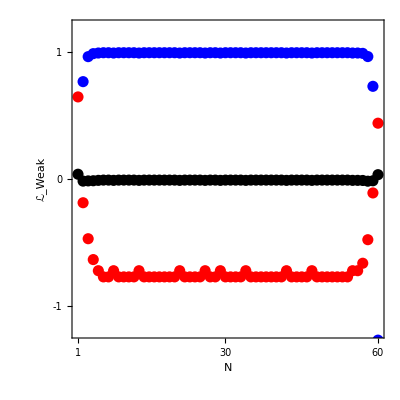

```mathematica
Show[ListPlot[list0,PlotRange->{{1,Lx},{-1.2,1.2}},Frame->True,PlotStyle-> {Red,PointSize[0.02]},Axes->False],
ListPlot[list1,PlotRange->{{1,Lx},{-1.2,1.2}},Frame->True,PlotStyle-> {Blue,PointSize[0.02]},Axes->False],
ListPlot[list0Trivial,PlotRange->{{1,Lx},{-1.2,1.2}},Frame->True,PlotStyle-> {Black,PointSize[0.02]},Axes->False],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 24,
FrameTicks->{ {{{-2,"-2"},{-1,"-1"},{0,"0"},{1,"1"},{2,"2"}},None},{{1,Lx/2,Lx},None}},
ImageSize-> 400,AspectRatio-> 1,
FrameLabel->{"N","ℒ_Weak"},RotateLabel->False]
```